```mathematica
Clear[a,μ, dr, eps,Q, kb, T]
μ=0.9*10^-2;
osseen[r_]:=1/(8 π μ)(IdentityMatrix[Length[r]]/Norm[r]+Outer[Times,r, r]/Norm[r]^3);
kernel[r_,a_]:=1/(((a/1.256)^2 π)^(3/2))Exp[(-r.r)/(a/1.256)^2];
nd[r_]:=(1/Norm[r])^3;

debye[r_]:=((eps kb T)/(2 nd[r] Q^2))^(1/2);

RPYl[r_,a_]:=1/(6 π μ a)(((3a)/(4 Norm[r])+a^3/(2 Norm[r]^3))IdentityMatrix[Length[r]]+((3a)/(4 Norm[r])-(3 a^3)/(2 Norm[r]^3))Outer[Times,r, r]/Norm[r]^2);
RPYs[r_,a_]:=1/(6 π μ a)((1-(9 Norm[r])/(32 a))IdentityMatrix[Length[r]]+((3 Norm[r])/(32 a))Outer[Times,r, r]/Norm[r]^2);
RPY[r_,a_]:=Which[Norm[r]≤2a,RPYs[r,a],Norm[r]> 2a,RPYl[r,a]];

dryTensor[r_,a_]:=1/(6 π μ a)IdentityMatrix[Length[r]];
coulomb[r_]:=Q^2/(4 π eps)r/Norm[r]^3;

coulombScreened[r_]:=Q^2/(4 π eps)(Exp[-Norm[r]/debye[r]](r+debye[r])r)/(Norm[r]^3 debye[r]);

p4[r_]:=Which[Abs[r]/dr≤1,(3-2 Abs[r]/dr+(1+4 Abs[r]/dr-4 r^2/dr^2)^(1/2))/8,
1<Abs[r]/dr≤2,(5-2 Abs[r]/dr-(-7+12 Abs[r]/dr-4 r^2/dr^2)^(1/2))/8,
 Abs[r]/dr ≥ 2,0];

p3[r_]:=Which[Abs[r]/dr≤0.5,(1+(1-3 r^2/dr^2)^(1/2))/3,
0.5<Abs[r]/dr≤1.5,(5-3 Abs[r]/dr-(-3(1- Abs[r]/dr)^2+1)^(1/2))/6,
 Abs[r]/dr ≥ 1.5,0];

peskin4[r_]:=p4[r[[1]]]p4[r[[2]]]p4[r[[3]]]/dr^3;
peskin3[r_]:=p3[r[[1]]]p3[r[[2]]]p3[r[[3]]]/dr^3;
```

2

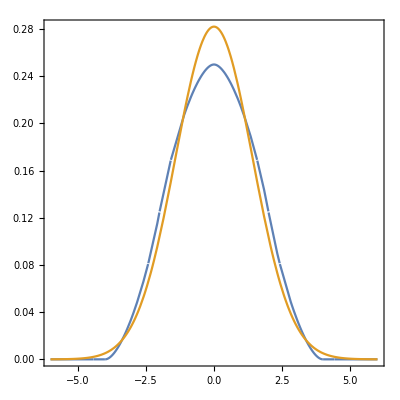

```mathematica
dr=2
Plot[{p4[r]/dr,1/(dr π^(1/2))Exp[-r^2/dr^2]},{r,-3 dr,3dr},Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
Integrate[1/(dr π^(1/2))Exp[-r^2/dr^2],{r,-∞,∞}]
Integrate[p4[r]/dr,{r,-∞,∞}]
```

1

1

```mathematica
T=295;
kb=1.38065*10^-16;
diff=0.5(1.17+1.33)*10^-5;
diffA=(1.17)*10^-5;
diffB=(1.33)*10^-5;
μ=0.01;
Q=1.6*10^-19;
eps = 692.96*10^-21;
aReal=(kb T)/(diff μ 6 π)
aA=(kb T)/(diffA μ 6 π)
aB=(kb T)/(diffB μ 6 π)

(aA+aB)/2
```

1.7286×10^-8

1.84679×10^-8

1.62462×10^-8

1.73571×10^-8

```mathematica
n=4*5*2*6.02*10^19
radsA=(1/n^(1/3))/aReal
radsB=0.55*(1/n^(1/3))/aReal
radsR=4.326863*10^-8/aReal
```

2.408×10^21

4.31605

2.37383

2.5031

```mathematica
velRPY[r_,a_,sep_]:= RPY[r,a].(coulomb[sep]);
velDry[r_,a_,sep_]:= dryTensor[r,a].coulomb[sep];

velRPYscreened[r_,a_,sep_]:= RPY[r,a].(coulombScreened[sep]);
velDryscreened[r_,a_,sep_]:= dryTensor[r,a].coulombScreened[sep];
```

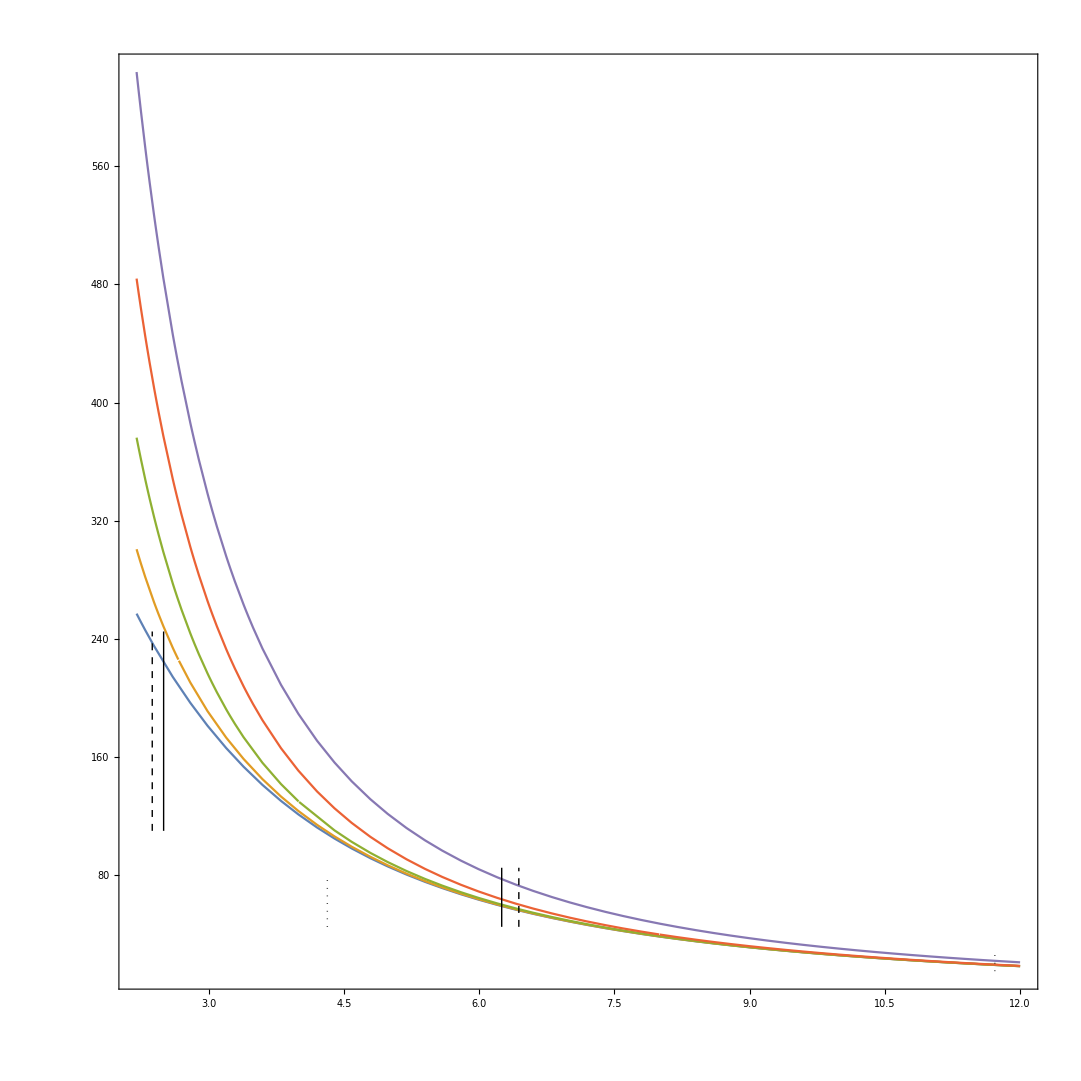

```mathematica
pa=Plot[{
velRPY[aReal{r,0,0},aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPY[aReal{r,0,0},1.3333aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPY[aReal{r,0,0},2aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPY[aReal{r,0,0},4aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]]}
,{r,2.2,12},PlotRange->All];
pb1=Graphics[{Line[{{6.25,45},{6.25,85}}],Dashed,Line[{{6.44,45},{6.44,85}}],Dotted,Line[{{11.72,15},{11.72,28}}]}];
pb2=Graphics[{Line[{{3.70,110},{3.70,245}}],Dashed,Line[{{3.77,110},{3.77,245}}],Dotted,Line[{{6.85,45},{6.85,80}}]}];
pb3=Graphics[{Line[{{2.5,110},{2.5,245}}],Dashed,Line[{{2.3738,110},{2.3738,245}}],Dotted,Line[{{4.3160,45},{4.3160,80}}]}];
Show[pa,pb1,pb3,Frame->True,AspectRatio->1,Axes->False]
```

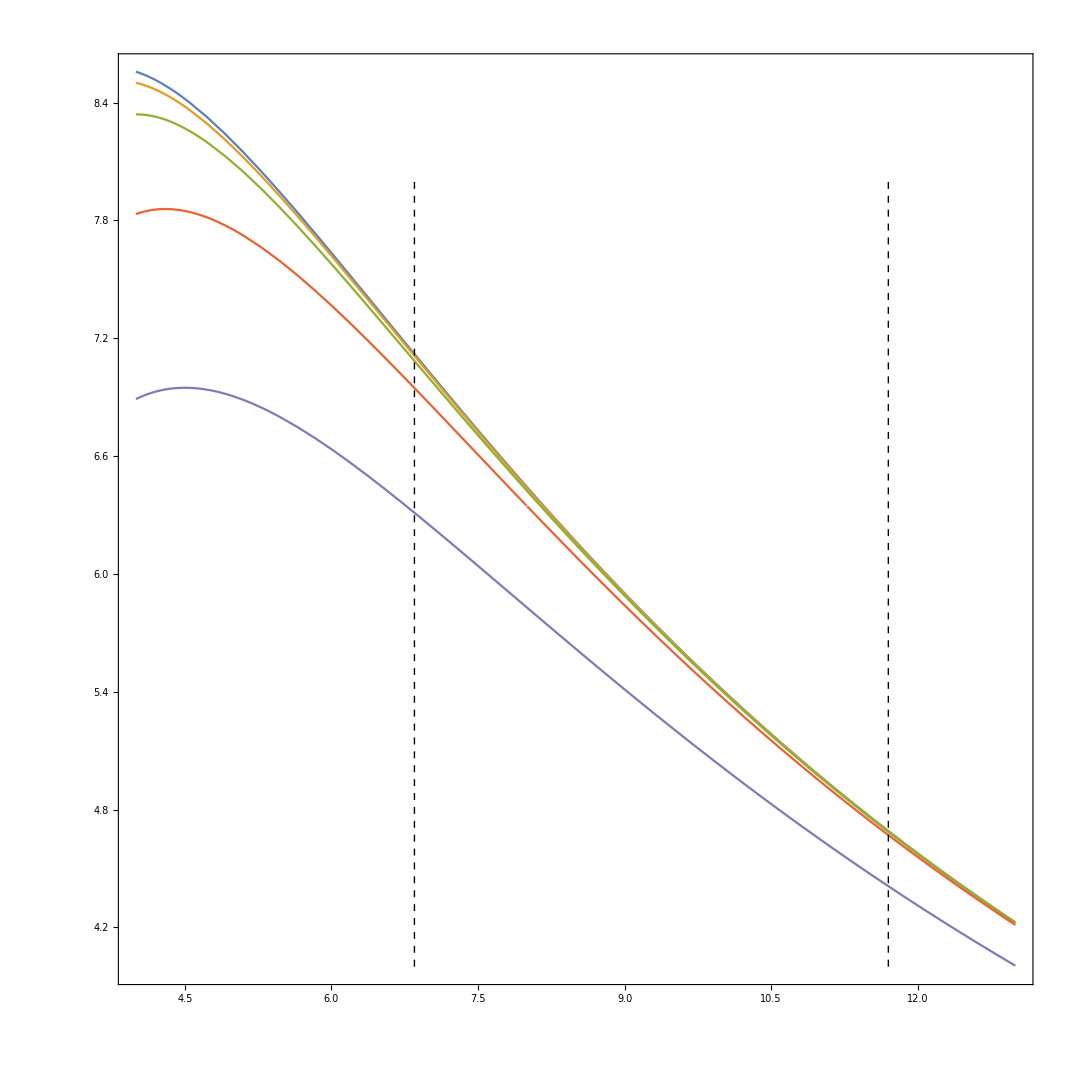

6.41282

7.28979

6.85131

6.85131

```mathematica
pa=Plot[{
velRPYscreened[aReal{r,0,0},aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPYscreened[aReal{r,0,0},1.3333aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPYscreened[aReal{r,0,0},2aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPYscreened[aReal{r,0,0},4aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]]}
,{r,4,13},PlotRange->All];
pb=Graphics[{Dashed,Line[{{6.85,4},{6.85,8}}],Line[{{11.7,4},{11.7,8}}]}];
Show[pa,pb,Frame->True,AspectRatio->1,Axes->False]
```

2.02515×10^-7

1.11383×10^-7

1.08×10^-7

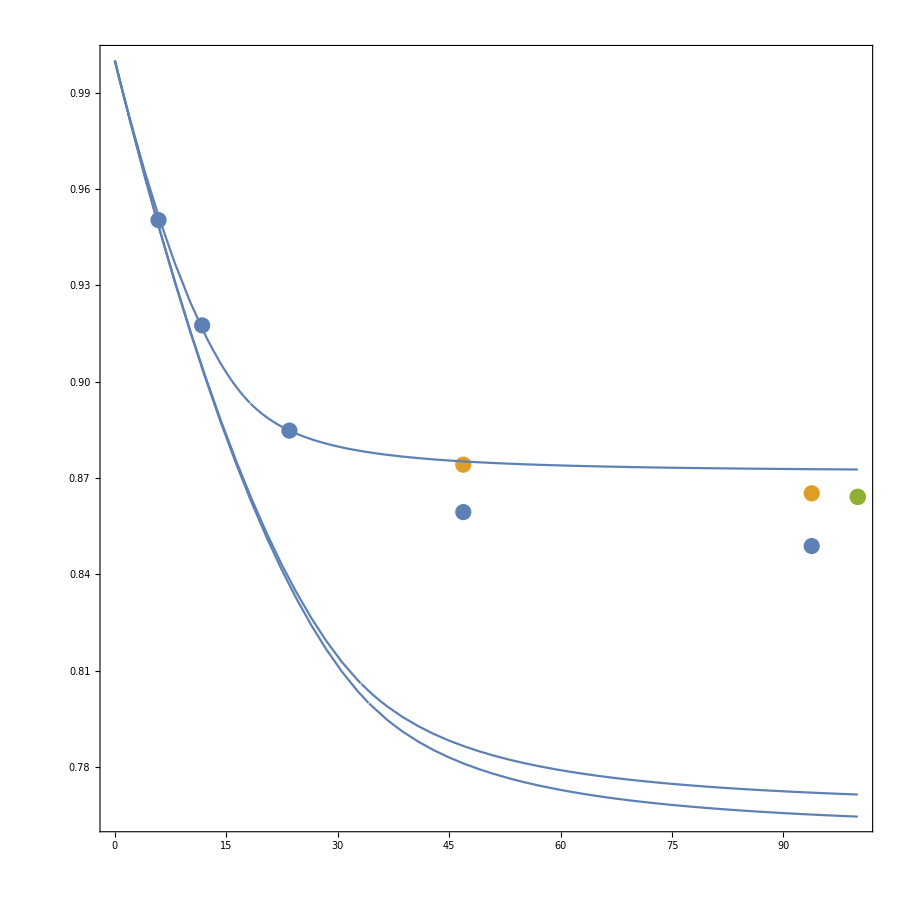

0.848837

6.85131

```mathematica
n=2*6.02*10^19;
radsA=(1/n^(1/3))
radsB=0.55*radsA
radsR=1.08*10^-7

rads=0.55radsM;
pointsZero={{93.8,8.03/9.46},{46.9,8.13/9.46},{23.5,8.37/9.46},{11.75,8.68/9.46},{5.88,8.99/9.46}};
pointsWeak={{93.8,7.77/8.98},{46.9,7.85/8.98}};
pointsTheory={{100,7.76/8.98}};
pointsStrong={{93.8,8.37/9.43},{46.9,8.41/9.43}};
pc=ListPlot[{pointsZero,pointsWeak,pointsTheory}];
pd=Plot[{
(velRPY[{radsA,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsA,0,0}][[1]]+velDry[{0,0,0},aReal,{radsA,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsA,0,0}][[1]])
},{per,0,100},PlotRange->All];
pe=Plot[{
(velRPY[{radsB,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsB,0,0}][[1]]+velDry[{0,0,0},aReal,{radsB,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsB,0,0}][[1]])
},{per,0,100},PlotRange->All];
pf=Plot[{
(velRPY[{radsR,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsR,0,0}][[1]]+velDry[{0,0,0},aReal,{radsR,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsR,0,0}][[1]])
},{per,0,100},PlotRange->All];
Show[pc,pd,pe,pf,PlotRange->All,Frame->True,AspectRatio->1,Axes->False]
```

1.18432×10^-7

6.51374×10^-8

6.39×10^-8

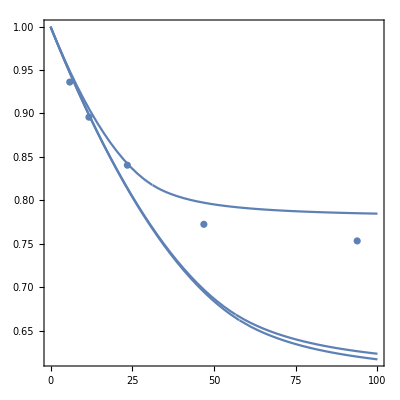

```mathematica
n=5*2*6.02*10^19;
radsA=(1/n^(1/3))
radsB=0.55*radsA
radsR=6.39*10^-8

pointsZero={{5.88,4.4/4.7},{11.75,4.21/4.70},{23.5,3.95/4.70},{46.9,3.63/4.70},{93.8,3.54/4.70}};
pc=ListPlot[{pointsZero}];
pd=Plot[{
(velRPY[{radsA,0,0},(kb T)/(per/100 diffA 6 μ π),-{radsA,0,0}][[1]]+velDry[{0,0,0},aReal,{radsA,0,0}][[1]])/(velDry[aReal{0,0,0},aReal,{radsA,0,0}][[1]])
},{per,0,100},PlotRange->All];
pe=Plot[{
(velRPY[{radsB,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsB,0,0}][[1]]+velDry[{0,0,0},aReal,{radsB,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsB,0,0}][[1]])
},{per,0,100},PlotRange->All];
pf=Plot[{
(velRPY[{radsR,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsR,0,0}][[1]]+velDry[{0,0,0},aReal,{radsR,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsR,0,0}][[1]])
},{per,0,100},PlotRange->All];
Show[pc,pd,pe,pf,Frame->True,PlotRange->All,AspectRatio->1,Axes->False]
```

7.46073×10^-8

4.1034×10^-8

4.32686×10^-8

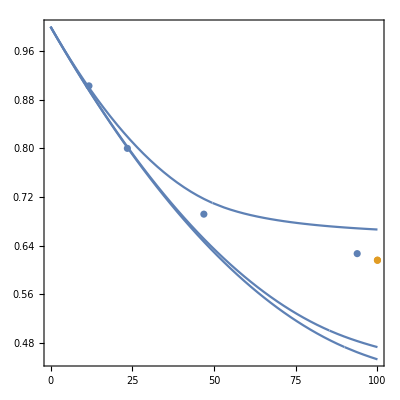

```mathematica
n=20*2*6.02*10^19;
radsA=(1/n^(1/3))
radsB=0.55*radsA
radsR=4.326863*10^-8

pointsZero={{11.75,1.67/1.85},{23.5,1.48/1.85},{46.9,1.28/1.85},{93.8,1.16/1.85}};
pointsTheory={{100,1.14/1.85}};
pc=ListPlot[{pointsZero,pointsTheory}];
pd=Plot[{
(velRPY[{radsA,0,0},(kb T)/(per/100 diffA 6 μ π),-{radsA,0,0}][[1]]+velDry[{0,0,0},aReal,{radsA,0,0}][[1]])/(velDry[aReal{0,0,0},aReal,{radsA,0,0}][[1]])
},{per,0,100},PlotRange->All];
pe=Plot[{
(velRPY[{radsB,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsB,0,0}][[1]]+velDry[{0,0,0},aReal,{radsB,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsB,0,0}][[1]])
},{per,0,100},PlotRange->All];
pf=Plot[{
(velRPY[{radsR,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsR,0,0}][[1]]+velDry[{0,0,0},aReal,{radsR,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsR,0,0}][[1]])
},{per,0,100},PlotRange->All];
Show[pc,pd,pe,pf,Frame->True,PlotRange->All,AspectRatio->1,Axes->False]
```

```mathematica
Q/(kb T)10^14 0.96*10^-7
```

37.7125

```mathematica
Q 10^14
```

0.000016

```mathematica
velRPY[aReal{10,0,0},aReal,-aReal{10,0,0}][[1]]
velRPY[aReal{0.000001,0,0},aReal,aReal{10,0,0}][[1]]
velField[aReal{0.000001,0,0},aReal,aReal{10,0,0}][[1]]
```

-3.68936

24.7608

4596.21

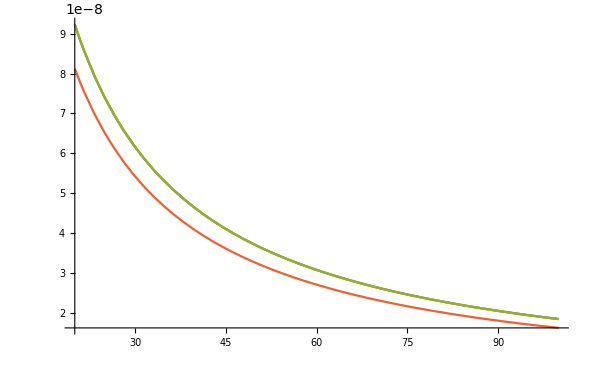

```mathematica
Plot[{(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),0.5((kb T)/((per/100 diffA) 6 μ π)+(kb T)/((0.881 per/100 diffB) 6 μ π)),((kb T)/((per/100 diffA) 6 μ π)),((kb T)/((per/100 diffB) 6 μ π))},{per,20,100}]
```

```mathematica
n=5*6.02*10^19;
(1/n^(1/3))
0.55(1/n^(1/3))
```

1.49215×10^-7

8.2068×10^-8

```mathematica
dataA=Import["/home/drladiges/kumonga/projects/FHDeX/exec/NN_test4/nearestNeighbour","Table"];
```

```mathematica
Mean[dataA[[-3;;-1]]]
```

{5.89375×10^-8,4.57637×10^-8,4.57889×10^-8,5.92056×10^-8,4.32686×10^-8}

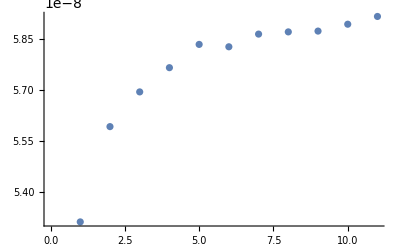

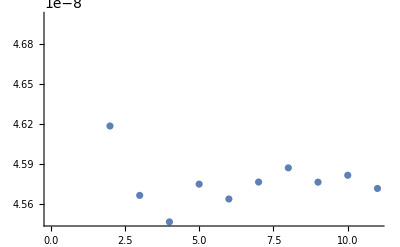

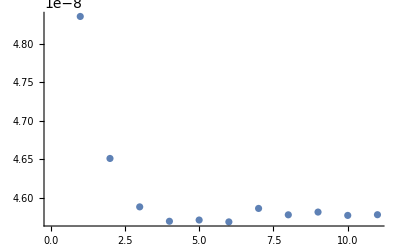

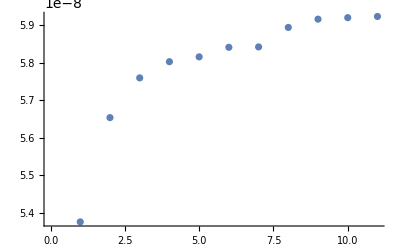

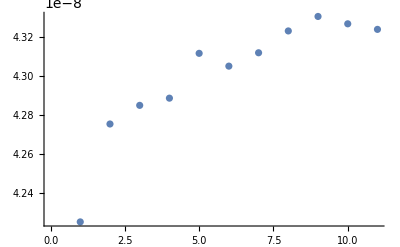

```mathematica
ListPlot[dataA[[All,1]]]
ListPlot[dataA[[All,2]]]
ListPlot[dataA[[All,3]]]
ListPlot[dataA[[All,4]]]
ListPlot[dataA[[All,5]]]
```

```mathematica
n=20*2*6.02*10^19;
radsA=(1/n^(1/3))/aReal
radsB=0.55*(1/n^(1/3))/aReal
```

4.31605

2.37383

{{{93.8,1/100},ErrorBar[3/500]},{{46.9,1/500},ErrorBar[7/1000]},{{23.5,1/50},ErrorBar[7/1000]},{{11.75,13/1000},ErrorBar[1/500]},{{5.88,19/500},ErrorBar[1/125]},{{0,43/500},ErrorBar[3/500]}}

{{{93.8,0.0347938},ErrorBar[0.00515464]},{{46.9,0.0476804},ErrorBar[0.00386598]},{{23.5,0.0786082},ErrorBar[0.00902062]},{{11.75,0.118557},ErrorBar[0.0115979]},{{5.88,0.158505},ErrorBar[0.0115979]},{{0,0.219072},ErrorBar[0.00515464]}}

{{{93.8,0.00128866},ErrorBar[0.00257732]},{{46.9,0.0115979},ErrorBar[0.00386598]},{{23.5,0.0115979},ErrorBar[0.00257732]},{{11.75,0.0708763},ErrorBar[0.00257732]},{{5.88,0.122423},ErrorBar[0.00257732]},{{0,0.157216},ErrorBar[0.00257732]}}

{{{93.8,-0.0152941},ErrorBar[0.00235294]},{{46.9,-0.0105882},ErrorBar[0.00352941]},{{23.5,0.00117647},ErrorBar[0.00235294]},{{11.75,0.0235294},ErrorBar[0.00235294]},{{5.88,0.0517647},ErrorBar[0.00235294]},{{0,0.109412},ErrorBar[0.00235294]}}

{{{0,0.407186},ErrorBar[0.00598802]},{{5.88,0.317365},ErrorBar[0.0598802]},{{11.75,0.260479},ErrorBar[0.00898204]},{{23.5,0.182635},ErrorBar[0.00598802]},{{46.9,0.0868263},ErrorBar[0.00598802]},{{93.8,0.0598802},ErrorBar[0.0149701]}}

{{{0,0.622807},ErrorBar[0.0175439]},{{5.88,0.491228},ErrorBar[0.0877193]},{{11.75,0.464912},ErrorBar[0.0263158]},{{23.5,0.298246},ErrorBar[0.0263158]},{{46.9,0.122807},ErrorBar[0.0175439]},{{93.8,0.0175439},ErrorBar[0.0263158]}}

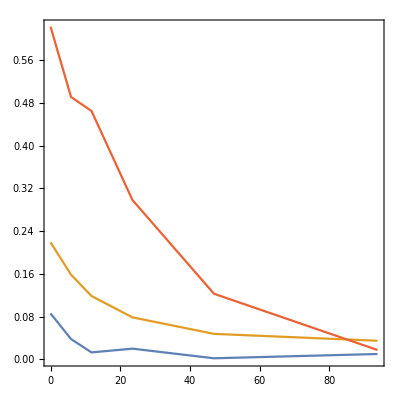

```mathematica
Needs["ErrorBarPlots`"];
points001err={{93.8,(1010-1000)/1000-(1010+0006-1000)/1000},
{46.9,(1002-1000)/1000-(1002+0007-1000)/1000},
{23.5,(1020-1000)/1000-(1020+0007-1000)/1000},
{11.75,(1013-1000)/1000-(1013+0002-1000)/1000},
{5.88,(1038-1000)/1000-(1038+0008-1000)/1000},
{0,(1086-1000)/1000-(1086+0006-1000)/1000}};
points001={{93.8,(1010-1000)/1000},
{46.9,(1002-1000)/1000},
{23.5,(1020-1000)/1000},
{11.75,(1013-1000)/1000},
{5.88,(1038-1000)/1000},
{0,(1086-1000)/1000}};
points001Plot=Table[{points001[[ii]],ErrorBar[-points001err[[ii,2]]]},{ii,1,Length[points001]}]
points01={{93.8,(8.03-7.76)/7.76},{46.9,(8.13-7.76)/7.76},{23.5,(8.37-7.76)/7.76},{11.75,(8.68-7.76)/7.76},{5.88,(8.99-7.76)/7.76},{0,(9.46-7.76)/7.76}};
points01err={{93.8,(8.03-7.76)/7.76-(8.03+0.04-7.76)/7.76},
{46.9,(8.13-7.76)/7.76-(8.13+0.03-7.76)/7.76},
{23.5,(8.37-7.76)/7.76-(8.37+0.07-7.76)/7.76},
{11.75,(8.68-7.76)/7.76-(8.68+0.09-7.76)/7.76},
{5.88,(8.99-7.76)/7.76-(8.99+0.09-7.76)/7.76},
{0,(9.46-7.76)/7.76-(9.46+0.04-7.76)/7.76}};
points01Plot=Table[{points01[[ii]],ErrorBar[-points01err[[ii,2]]]},{ii,1,Length[points01]}]

points01w={{93.8,(7.77-7.76)/7.76},{46.9,(7.85-7.76)/7.76},{23.5,(7.85-7.76)/7.76},{11.75,(8.31-7.76)/7.76},{5.88,(8.71-7.76)/7.76},{0,(8.98-7.76)/7.76}};
points01werr={{93.8,(7.77-7.76)/7.76-(7.77+0.02-7.76)/7.76},
{46.9,(7.85-7.76)/7.76-(7.85+0.03-7.76)/7.76},
{23.5,(7.85-7.76)/7.76-(7.85+0.02-7.76)/7.76},
{11.75,(8.31-7.76)/7.76-(8.31+0.02-7.76)/7.76},
{5.88,(8.71-7.76)/7.76-(8.71+0.02-7.76)/7.76},
{0,(8.98-7.76)/7.76-(8.98+0.02-7.76)/7.76}};
points01wPlot=Table[{points01w[[ii]],ErrorBar[-points01werr[[ii,2]]]},{ii,1,Length[points01w]}]

points01s={{93.8,(8.37-8.50)/8.50},{46.9,(8.41-8.50)/8.50},{23.5,(8.51-8.50)/8.50},{11.75,(8.70-8.50)/8.50},{5.88,(8.94-8.50)/8.50},{0,(9.43-8.50)/8.50}};
points01serr={{93.8,(8.37-8.50)/8.50-(8.37+0.02-8.50)/8.50},
{46.9,(8.41-8.50)/8.50-(8.41+0.03-8.50)/8.50},
{23.5,(8.51-8.50)/8.50-(8.51+0.02-8.50)/8.50},
{11.75,(8.51-8.50)/8.50-(8.51+0.02-8.50)/8.50},
{5.88,(8.70-8.50)/8.50-(8.70+0.02-8.50)/8.50},
{0,(8.94-8.50)/8.50-(8.94+0.02-8.50)/8.50}};
points01sPlot=Table[{points01s[[ii]],ErrorBar[-points01serr[[ii,2]]]},{ii,1,Length[points01s]}]


points05={{0,(4.7-3.34)/3.34},
{5.88,(4.4-3.34)/3.34},
{11.75,(4.21-3.34)/3.34},
{23.5,(3.95-3.34)/3.34},
{46.9,(3.63-3.34)/3.34},
{93.8,(3.54-3.34)/3.34}};
points05err={{0,(4.7-3.34)/3.34-(4.7+0.02-3.34)/3.34},{5.88,(4.4-3.34)/3.34-(4.4+0.2-3.34)/3.34},
{11.75,(4.21-3.34)/3.34-(4.21+0.03-3.34)/3.34},
{23.5,(3.95-3.34)/3.34-(3.95+0.02-3.34)/3.34},
{46.9,(3.63-3.34)/3.34-(3.63+0.02-3.34)/3.34},
{93.8,(3.54-3.34)/3.34-(3.54+0.05-3.34)/3.34}};
points05Plot=Table[{points05[[ii]],ErrorBar[-points05err[[ii,2]]]},{ii,1,Length[points05]}]

points20={{0,(1.85-1.14)/1.14},{5.88,(1.7-1.14)/1.14},{11.75,(1.67-1.14)/1.14},{23.5,(1.48-1.14)/1.14},{46.9,(1.28-1.14)/1.14},{93.8,(1.16-1.14)/1.14}};
points20err={{0,(1.85-1.14)/1.14-(1.85+0.02-1.14)/1.14},
{5.88,(1.7-1.14)/1.14-(1.7+0.1-1.14)/1.14},
{11.75,(1.67-1.14)/1.14-(1.67+0.03-1.14)/1.14},
{23.5,(1.48-1.14)/1.14-(1.48+0.03-1.14)/1.14},
{46.9,(1.28-1.14)/1.14-(1.28+0.02-1.14)/1.14},
{93.8,(1.16-1.14)/1.14}-(1.16+0.03-1.14)/1.14};
points20Plot=Table[{points20[[ii]],ErrorBar[-points20err[[ii,2]]]},{ii,1,Length[points20]}]
ListPlot[{points001,points01,points05Plot,points20},Joined->True,PlotRange->All,Axes->False,Frame->True,AspectRatio->1]
```

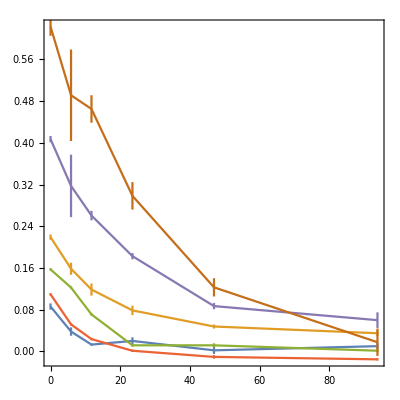

```mathematica
ErrorListPlot[{points001Plot,points01Plot,points01wPlot,points01sPlot,points05Plot,points20Plot},Joined->True,PlotRange->All,Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
dims={13.06*10^-7,13.06*10^-7,6.53*10^-7};
domainParts=87;
wallPartsX = 40;
wallPartsZ = 20;
wallTotal = wallPartsX*wallPartsZ; 

xCell=dims[[1]]/wallPartsX;
zCell =xCell;

wallPosBottom = Flatten[Table[{xCell/2+xCell*ii,0.25*dims[[2]],xCell/2+zCell*jj},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosTop = Flatten[Table[{xCell/2+xCell*ii,0.75dims[[2]],xCell/2+zCell*jj},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPos=Join[wallPosBottom,wallPosTop];

images=1;
(*wallPosPeriodicBottom=Flatten[Table[Flatten[Table[{xCell/2+xCell*ii+oo*dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj+pp*dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1],{oo,-images,images},{pp,-images,images}],1];
wallPosPeriodicTop=Flatten[Table[Flatten[Table[{xCell/2+xCell*ii+oo*dims[[1]],0.75*dims[[2]],xCell/2+zCell*jj+pp*dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1],{oo,-images,images},{pp,-images,images}],1];
wallPosPeriodic=Thread[wallPosPeriodicBottom,wallPosPeriodicTop]*)

wallPosPeriodic=Flatten[Table[Join[Flatten[Table[{xCell/2+xCell*ii+oo*dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj+pp*dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1],Flatten[Table[{xCell/2+xCell*ii+oo*dims[[1]],0.75*dims[[2]],xCell/2+zCell*jj+pp*dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1]],{oo,-images,images},{pp,-images,images}],1];

(*wallPosBottomGL = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGR = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGF = Flatten[Table[{xCell/2+xCell*ii,0.25*dims[[2]],xCell/2+zCell*jj+dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGB = Flatten[Table[{xCell/2+xCell*ii,0.25*dims[[2]],xCell/2+zCell*jj-dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGBL = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj-dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGBR = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj-dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGFL = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj+dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGFR = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj+dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];

wallPosBottomGL2 = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGR2 = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGF2 = Flatten[Table[{xCell/2+xCell*ii,0.25*dims[[2]],xCell/2+zCell*jj+dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGB2 = Flatten[Table[{xCell/2+xCell*ii,0.25*dims[[2]],xCell/2+zCell*jj-dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGBL2 = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj-dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGBR2 = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj-dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGFL = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj+dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGFR = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj+dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];*)
```

```mathematica
Length[wallPosPeriodic]
```

9

```mathematica
Length[mob]
testForce=Join[{1},Table[0,{ii,1,Length[mob]-1}]];
```

4800

```mathematica
aa=1.255*xCell;
μ=0.9*10^-2;
mob=Sum[ArrayFlatten[Table[Table[If[wallPos[[jj]]-wallPosPeriodic[[pp,ii]]=={0,0,0},dryTensor[{0,0,0},aa],RPY[wallPos[[jj]]-wallPosPeriodic[[pp,ii]],aa]],{ii,1,Length[wallPos]}],{jj,1,Length[wallPos]}]],{pp,{1,2,4,5,6,7,8,9}}]//Evaluate;
(*mobGL=ArrayFlatten[Table[Table[RPY[wallPosBottom[[jj]]-wallPosBottomGL[[ii]],aa],{ii,1,Length[wallPosBottomGL]}],{jj,1,Length[wallPosBottom]}]];*)
```

```mathematica
mobInv=Inverse[mob];
```

```mathematica
vel=mob.testForce;
force=mobInv.vel;
Norm[force]
```

1.

```mathematica
mob
```

{{1.43856×10^8,0.,0.,1.11618×10^8,0.,0.,7.9379×10^7,0.,0.,5.04008×10^7,0.,0.,3.60728×10^7,0.,0.,2.82184×10^7,0.,0.,2.32257×10^7,0.,0.,1.97581×10^7,0.,0.,1.72033×10^7,0.,0.,1.524×10^7,0.,0.,1.36827×10^7,0.,0.,4734,5.32335×10^6,1.1772×10^6,529739.,5.27681×10^6,1.16065×10^6,580326.,5.22647×10^6,1.14281×10^6,628547.,5.17262×10^6,1.12379×10^6,674275.,5.11556×10^6,1.10371×10^6,717411.,5.05558×10^6,1.08268×10^6,757878.,4.99299×10^6,1.06083×10^6,795624.,4.92809×10^6,1.03828×10^6,830620.,4.86117×10^6,1.01513×10^6,862860.,4.79253×10^6,991505.,892354.,4.72245×10^6,967510.,919135.},4798,{1}}
 |  |  |  |

```mathematica
dryTensor[{0,0,0},aa]
```

{{1.43856×10^8,0.,0.},{0.,1.43856×10^8,0.},{0.,0.,1.43856×10^8}}

```mathematica
6π μ aa 1.438564888238055*^8
```

1.

```mathematica
NotebookDirectory[]
```

/home/drladiges/projects/FHDeX/exec/notebooks/